```mathematica
Needs["NumericalCalculus`"]
NN = 500;
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];

dd = 10.0;
func1 [ s_ ] := 1/NN∑_(k=0)^(NN-1) Log [ dd + ( s - circ[[k+1]])Conjugate[ s - circ [[ k+1 ]] ] ]
```

```mathematica
func2 [ s_ ] := Log [ dd + s^2 + 1]
```

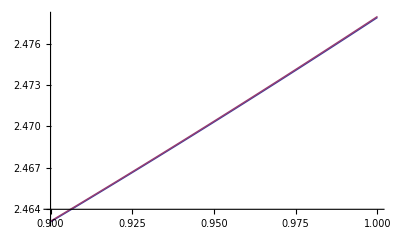

```mathematica
Plot[ {func1[s], func2[s] - (s/(dd + (s^2 + 1)))^2}, {s, 0.9, 1.}]
```